```mathematica
(*Зададим данную функцию*)
f[x_]=Exp[x]*Cos[2*x]-Sin[3*x];
(*Зададим отрезок интерполяции*)
a=0;
b=Pi;
(*Построим график данной функции*)
G=Plot[f[x],{x,a,b}];
(*Найдем производную первого порядка для данной функции*)
f1[x_]=D[f[x],x];
(*Найдем производную второго порядка для данной функции*)
f2[x_]=D[f[x],{x,2}];
```

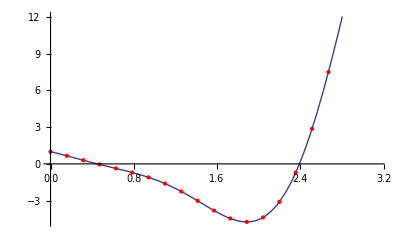

```mathematica
(*Зададим количество частичных отрезков*)
n=20;
(*Зададим шаг разбиения*)
h=(b-a)/n;
(*Построим таблично заданную функцию*)
X=Table[a+k*h,{k,0,n}];
Y=Table[f[X[[k]]],{k,1,n+1}];
XY=Table[{X[[k]],Y[[k]]},{k,1,n+1}];
GPoints=ListPlot[XY,PlotStyle->Red];
Show[G,GPoints]
```

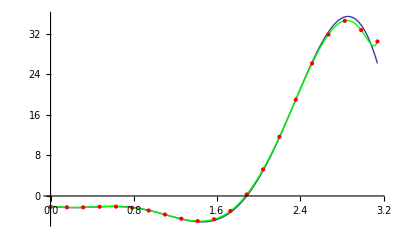

```mathematica
(*Построим таблицу значений производной первого порядка*)
Y1=Table[(Y[[k+1]]-Y[[k-1]])/(2*h),{k,2,n}];
PrependTo[Y1,(Y[[2]]-Y[[1]])/h];
AppendTo[Y1,(Y[[n]]-Y[[n+1]])/(-h)];
(*Выполним интерполяцию найденной производной первого порядка*)
y1[x_]=Sum[Y1[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Построим графики точной производной и приближенной производной первого порядка данной функции в одной системе координат*)
G1=Plot[f1[x],{x,a,b}];
XY1=Table[{X[[k]],Y1[[k]]},{k,1,n+1}];
G1Points=ListPlot[XY1,PlotStyle->Red];
GY1=Plot[y1[x],{x,a,b},PlotStyle->Green];
Show[G1,GY1,G1Points]
```

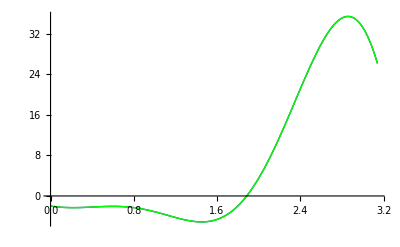

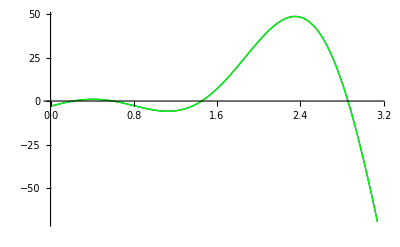

```mathematica
(*Построим многочлен Лагранжа для данной функции*)
L[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Найдем производную первого порядка построенного многочлена Лагранжа*)
L1[x_]=D[L[x],x];
(*Найдем производную второго порядка построенного многочлена Лагранжа*)
L2[x_]=D[L[x],{x,2}];
GL1=Plot[L1[x],{x,a,b},PlotStyle->Green];
GL2=Plot[L2[x],{x,a,b},PlotStyle->Green];
G2=Plot[f2[x],{x,a,b}];
Show[G1,GL1]
Show[G2,GL2]
```

-11 ⅇ^x Cos[2 x]+27 Cos[3 x]+2 ⅇ^x Sin[2 x]

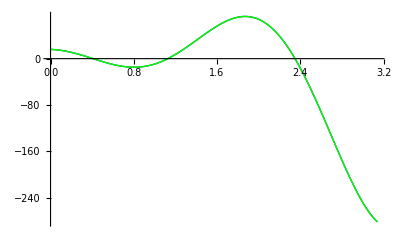

```mathematica
L3[x_]=D[L[x],{x,3}];
GL3=Plot[L3[x],{x,a,b},PlotStyle->Green];
f3[x_]=D[f[x],{x,3}]
G3=Plot[f3[x],{x,a,b}];
Show[G3,GL3]
```